```mathematica
Manipulate[
Module[{t,w,L,P,Ac,k,u,ν,ρ,μ,ka,Cp,Pr,Rex,h,Tb,m,qf,T,col,xT,rectangular,pin,legend},
t=0.0015;(*m*)
w=0.02;
L:=length/1000;

If[fin==1,
{P:=2*w+2*t;Ac:=w*t;},
{P:=π*t;Ac:=π*(t/2)^2;}];

(*therm. data*)
k:=Which[
mat==1,14,(*s.steel*)
mat==2,60.5,(*carbon steel*)
mat==3,80.2,(*iron*)
mat==4,110,(*brass*)
mat==5,237,(*aluminum*)
mat==6,401(*copper*)
];(*W/m/K*)

(*air properties*)
u=2;(*m/s*)
ν=1.71*^-5;(*m2/s*)
ρ=1.164;(*kg/m3*)
μ:=ν*ρ;(*N s/m2*)
ka=0.0264;(*W/m/K*)
Cp=1005;(*J/kg/K*)

Pr:=(Cp*μ)/ka;
Rex:=(u*If[fin==1,w,t])/ν;
h:=If[fin==1,
ka/w*0.664*Rex^(1/2)*Pr^(1/3),
If[Rex<4000,ka/t*0.683*Rex^0.466*Pr^(1/3),ka/t*0.193*Rex^0.618*Pr^(1/3)]
];

(*heat, temperature*)
Tb=500;(*K*)
m:=√((2*h)/(k*t));
qf:=(Tb-Ta)*√(h*P*k*Ac)*Tanh[m*L];
T[x_]:=(Tb-Ta)*Cosh[m*(L-x)]/Cosh[m*L]+Ta;

col[x_]:=ColorData["TemperatureMap"][Rescale[T[x],{307.3,Tb}]];

(*xT:=Evaluate@Interpolation[Transpose[{Range[500,300,-5],Evaluate@Table[x/.Quiet@FindRoot[250*(1+0.229*Cosh[107.7*(0.02-x)])==t,{x,0}],{t,300,500,5}]}]];*)
xT:=Quiet@Interpolation[Table[{250+57.25*Cosh[107.7*(1/50-x)],x},{x,0,0.02,0.001}]];

rectangular:=Show[Graphics3D[{col[0],Cuboid[{-0.0025,-w/2,-w/2},{0,w/2,w/2}]}],
RegionPlot3D[z<t,{x,0,L},{y,-w/2,w/2},{z,0,t},Mesh->None,ColorFunction->(col[#1]&),ColorFunctionScaling->False]];

pin:=Show[Graphics3D[{{col[0],Cuboid[{-0.0025,-w/2,-w/2},{0,w/2,w/2}]},{col[L],Cylinder[{{0.999*L,0,0},{L,0,0}},t/2]}}],
ParametricPlot3D[{x,t/2*Sin[θ],t/2*Cos[θ]},{θ,0,2*π},{x,0,L},Mesh->None,ColorFunction->(col[#1]&),ColorFunctionScaling->False]];

(*legend:=DensityPlot[xT[y],{x,0,0.02},{y,307.3,500},ColorFunction->ColorData[{"TemperatureMap","Reverse"}],PlotPoints->30,
Epilog->{Text[col[L],{0,T[L]},{1,0}]},
PlotRangePadding->{{0.0025,0},0},AspectRatio->Full,ImageSize->{150,350}];*)

legend:=DensityPlot[250+57.25*Cosh[107.7*(1/50-x)],{x,0,0.02},{y,307.3,500},ColorFunction->"TemperatureMap",PlotPoints->30,AspectRatio->Full,ImageSize->{150,350}];

Grid[{{
Show[Switch[fin,1,rectangular,2,pin],Boxed->False,ViewPoint->{2,-2,1},Lighting->"Neutral",ImageSize->{300,350}],
legend
}}]

(*Plot[250+57.25*Cosh[107.7*(1/50-x)],{x,0,0.02},PlotLabel->250+57.25*Cosh[107.7*(1/50-0.02)]]*)
(*Table[{250+57.25*Cosh[107.7*(1/50-x)],x},{x,0,0.02,0.001}]*)
],
Column[{
Row[{
Control[{{fin,1,"fin type:"},{1->" rectangular ",2->" pin "},Setter}],Spacer[20],
Control[{{mat,1,"material:"},{1->"stainless steel",2->"carbon steel",3->"iron",4->"brass",5->"aluminum",6->"copper"},PopupMenu}]
}],
Control[{{length,10,"fin length (mm)"},5,20,1,Appearance->"Labeled"}],
Control[{{Ta,300,"ambient temperature (K)"},250,350,1,Appearance->"Labeled"}]
}]
]
```

```mathematica
(250+57.25*Cosh[107.7*(1/50-x)])/.x->0.02
```

307.25

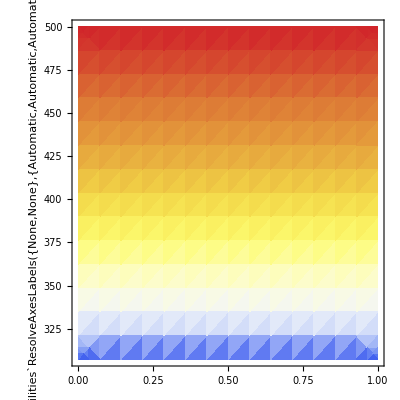

```mathematica
Module[{T,L1,L2,L3,fxT},
T[x_]:=250+57.25*Cosh[107.7*(1/50-x)];

L1:=Table[{T[x],x},{x,0,0.02,0.001}];
L2:=Table[T[x],{x,0,0.02,0.001}];
L3:=Table[x,{x,0,0.02,0.001}];

(*fxT:=Interpolation[Transpose[{Reverse[L2],L3}]];*)

fxT:=Interpolation[Table[{T[x],0.02-x},{x,0,0.02,0.001}]];

DensityPlot[fxT[temp],{x,0,1},{temp,307.3,500},ColorFunction->"TemperatureMap"]
]
```

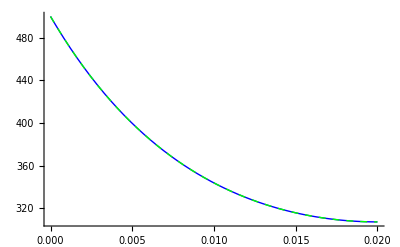

```mathematica
Plot[{
250*(1+0.229*Cosh[107.7*(0.02-x)]),
250+57.25*Cosh[107.7*(1/50-x)]
},{x,0,0.02},PlotStyle->{{Thick,Blue},{Thick,Dashed,Green}}]
```

```mathematica
Table[{250+57.25*Cosh[107.7*(1/50-x)],x},{x,0,0.02,0.001}]
```

{{500.048,0.},{475.234,0.001},{453.035,0.002},{433.193,0.003},{415.479,0.004},{399.686,0.005},{385.63,0.006},{373.15,0.007},{362.099,0.008},{352.35,0.009},{343.789,0.01},{336.317,0.011},{329.847,0.012},{324.305,0.013},{319.625,0.014},{315.753,0.015},{312.645,0.016},{310.264,0.017},{308.583,0.018},{307.582,0.019},{307.25,0.02}}